```mathematica
tau=10;
sinExp[t_]:=ⅇ^(-t/tau);
```

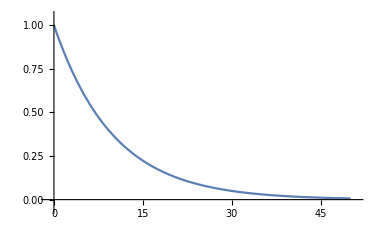

```mathematica
Plot[sinExp[t], {t, 0, 50}]
```

```mathematica
gSinExp[w_]:=(∫_0^100 sinExp[t] Cos[w t]ⅆt)/(∫_0^100 sinExp[t]ⅆt);
```

```mathematica
sSinExp[w_]:=(∫_0^100 sinExp[t] Sin[w t]ⅆt)/(∫_0^100 sinExp[t]ⅆt);
```

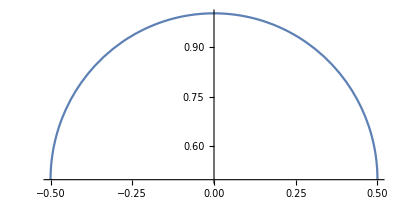

```mathematica
ParametricPlot[{s[w], g[w]}, {w, -0.1, 0.1}]
```

```mathematica
cen=20;
bw=60;
gauss[t_]:=ⅇ^(-(t-cen)^2/(2 bw^2));
```

```mathematica
gGauss[w_]:=(∫_-200^200 gauss[t] Cos[w t]ⅆt)/(∫_-200^200 gauss[t]ⅆt)
sGauss[w_]:=(∫_-200^200 gauss[t] Sin[w t]ⅆt)/(∫_-200^200 gauss[t]ⅆt)
```

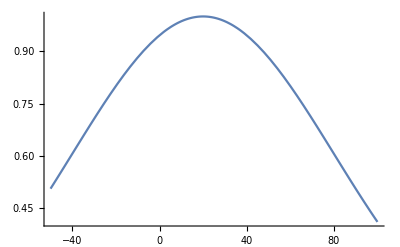

```mathematica
Plot[gauss[t], {t, -50, 100},PlotRange->Full]
```

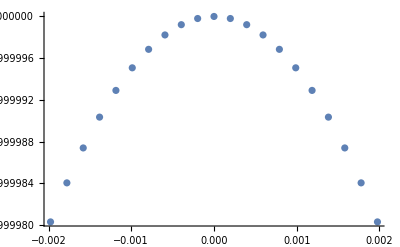

```mathematica
ListPlot[Table[{sGauss[w], gGauss[w]}, {w, -0.0001, 0.0001, 0.00001}]]
```

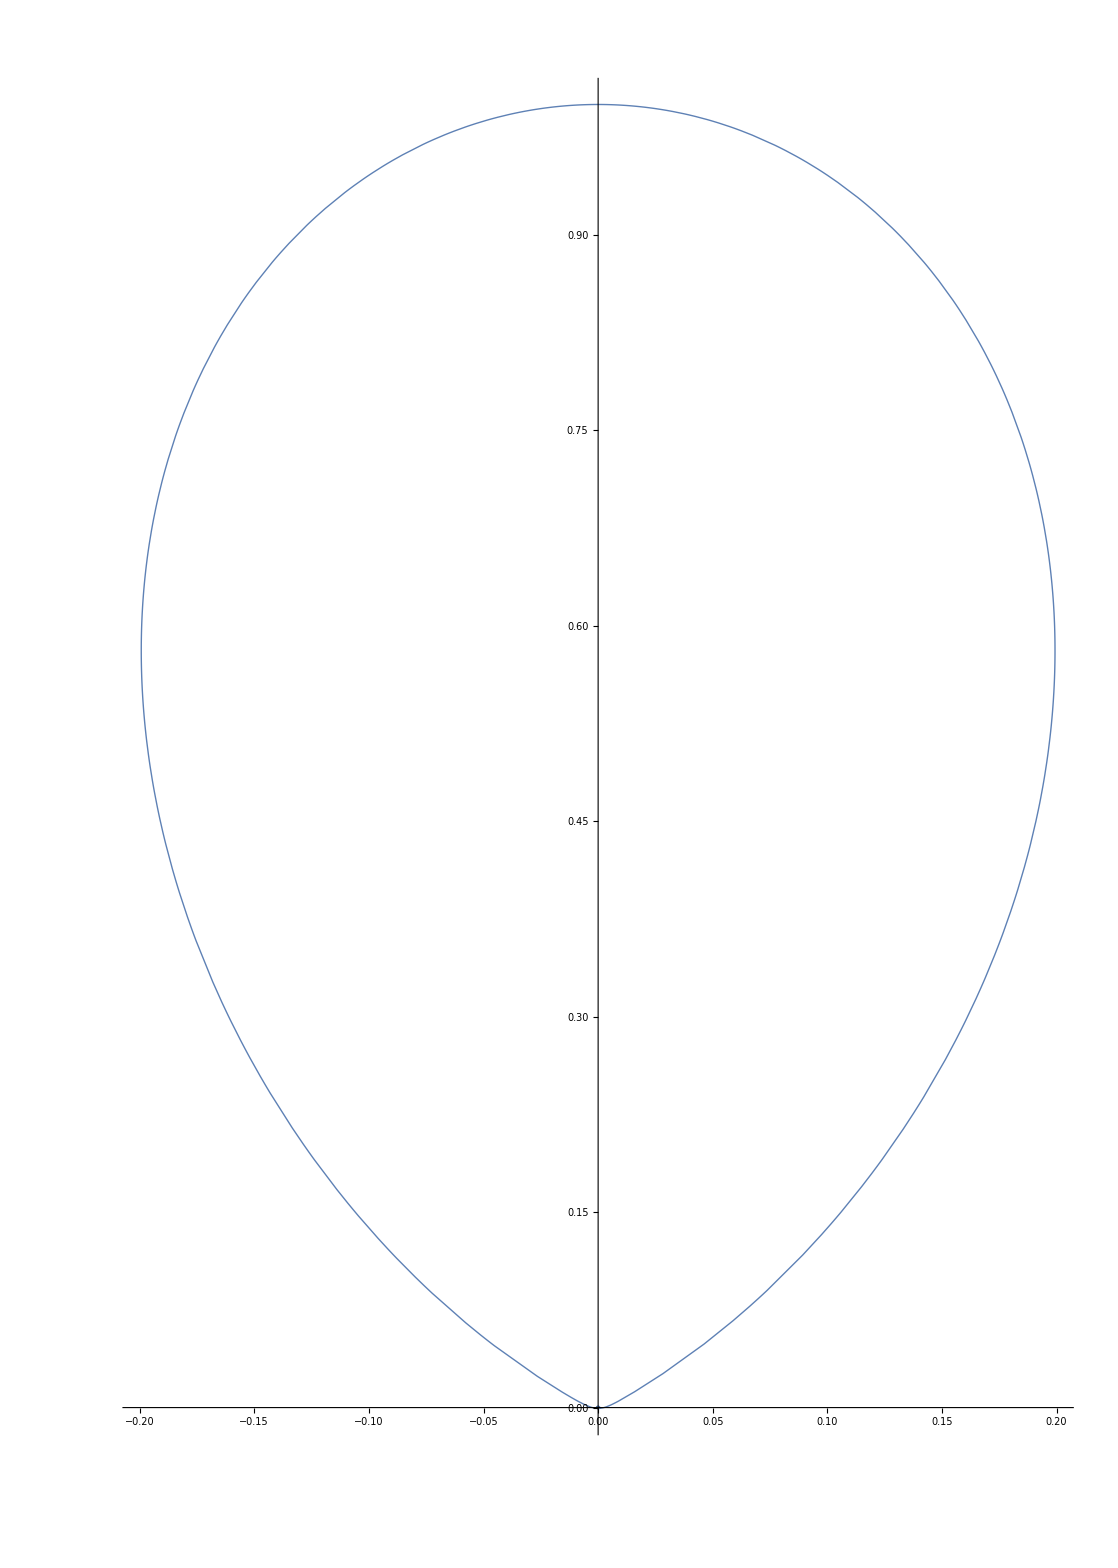

```mathematica
ParametricPlot[{sGauss[w], gGauss[w]}, {w, -0.1, 0.1}, PlotStyle->Thick, PlotPoints->50]
```

```mathematica
xpm[t_]:=t ⅇ^(-t^2/bw);
```

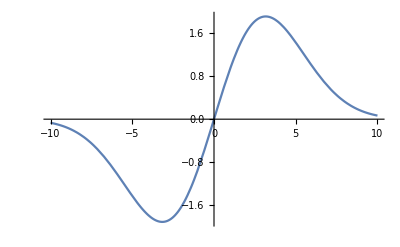

```mathematica
Plot[xpm[t], {t, -10, 10}]
```

```mathematica
gXpm[w_]:=(∫_-50^50 xpm[t] Cos[w t]ⅆt)/(∫_0^100 gauss[t]ⅆt);
sXpm[w_]:=(∫_-50^50 xpm[t] Sin[w t]ⅆt)/(∫_0^100 gauss[t]ⅆt);
```

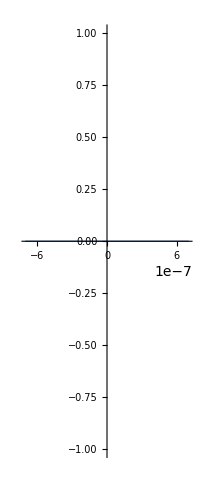

```mathematica
ParametricPlot[{sXpm[w], gXpm[w]}, {w, -0.01, 0.01}, PlotStyle->Thick]
```

```mathematica
comp[t_]:=sinExp[t]+gauss[t]+xpm[t]
```

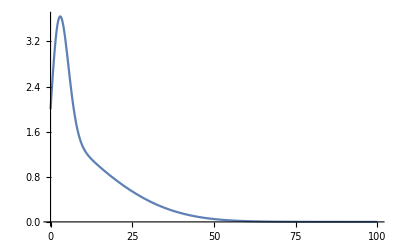

```mathematica
Plot[comp[t], {t, 0, 100}, PlotRange->Full]
```

```mathematica
gcomp[w_]:=(∫_-50^50 comp[t] Cos[w t]ⅆt)/(∫_-50^50 comp[t]ⅆt);
scomp[w_]:=(∫_-50^50 comp[t] Sin[w t]ⅆt)/(∫_-50^50 comp[t]ⅆt);
```

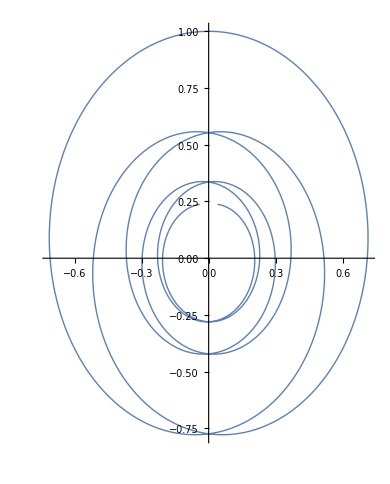

```mathematica
ParametricPlot[{scomp[w], gcomp[w]}, {w, -0.4, 0.4}, PlotStyle->Thick,PlotRange->Full]
```

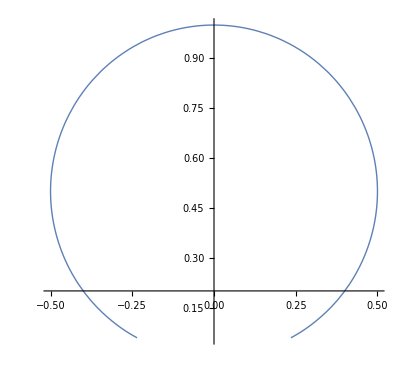

```mathematica
ParametricPlot[{sSinExp[w]+sGauss[w]+sXpm[w], gSinExp[w]+gGauss[w]+gXpm[w]}, {w, -0.4, 0.4}, PlotStyle->Thick,PlotRange->Full]
```